# Solving for amplitude

```mathematica
ClearAll["Global`*"]
ω1 = 2 Sin[Pi/2 y];
FullSimplify[Solve[S == A^2(ω1)^2 β 1/(4 y^2)(1+ w 3 β (ω1)^2 A^2/8),A],{y>0,S>0,β>0}]
```

```mathematica
A =(√(((-1+√(1+6 S w y^2)) Csc[(π y)/2]^2)/(w β)))/(√3);
FullSimplify[Series[A,{y,0,3}]]
```

General::ivar: 1/(1+n) is not a valid variable.

Series[(√(((-1+√(1+(6 S w)/(1+n)^2)) Csc[π/(2+2 n)]^2)/(w β)))/(√3),{1/(1+n),0,3}]

```mathematica
Continuum Limit;
ClearAll["Global`*"]
qnp1 = q+a qx + a^2/2 qxx + a^3/6 qxxx + a^4/24 qxxxx;
qnm1 = q+-a qx + a^2/2 qxx - a^3/6 qxxx + a^4/24 qxxxx;
Series[FullSimplify[qnp1+qnm1-2q+β((qnp1-q)^3-(q-qnm1)^3)],{a,0,5}]
```

qxx a^2+1/12 (qxxxx+36 qx^2 qxx β) a^4+O[a]^6

```mathematica
mKdV Solitons
Clear[δ,c, ζ]
FullSimplify[DSolve[gg'[x] Sqrt[ζ]==gg[x] Sqrt[(-1/6 gg[x]^2+c)],gg[x],x]]
```

```mathematica
Integrate[1/(g Sqrt[v/ζ-1/(6 ζ) g^2]),g]
```

```mathematica
FullSimplify[Solve[ξ-C ==-(√ζ ArcTanh[(√(-g^2/(6 ζ)+v/ζ) √ζ)/(√v)])/(√v),g]]
```

```mathematica
Simplify[D[-Sqrt[6 c]Sech[Sqrt[c/ζ](x-c t)],x]]
```

```mathematica
Sholl and Henry Pertubation
```

```mathematica
ClearAll["Global`*"]
B51 = (3 A5311 ((Ω3-Ω5) (Ω3+Ω5) ((175 A32+71 A33) Ω1^4-8 (4 A32+3 A33) Ω1^2 Ω5^2+(A32+A33) Ω5^4) (16 Ω1^4+(Ω3^2-Ω5^2)^2-8 Ω1^2 (Ω3^2+Ω5^2))+A31 (225 Ω1^6-259 Ω1^4 Ω5^2+35 Ω1^2 Ω5^4-Ω5^6) (8 Ω1^4+(Ω3^2-Ω5^2)^2-2 Ω1^2 (Ω3^2+3 Ω5^2))))/((Ω3-Ω5) (-2 Ω1+Ω3-Ω5) (2 Ω1+Ω3-Ω5) (-5 Ω1+Ω5) (-3 Ω1+Ω5) (-Ω1+Ω5) (Ω1+Ω5) (3 Ω1+Ω5) (5 Ω1+Ω5) (Ω3+Ω5) (-2 Ω1+Ω3+Ω5) (2 Ω1+Ω3+Ω5));

B52 = (3 (3 A32+A33) A5311)/(4 (Ω1^2-Ω5^2));
B53 = (3 (A32+2 A33) A5311)/(36 Ω1^2-4 Ω5^2);
B54 = (3 A33 A5311)/(100 Ω1^2-4 Ω5^2);
B55 = (3 A31 A5311)/(2 (Ω3^2-Ω5^2));
B56 = (3 A31 A5311)/(4 (-2 Ω1+Ω3)^2-4 Ω5^2);
B57 = (3 A31 A5311)/(4 (2 Ω1+Ω3)^2-4 Ω5^2);

a52 = B51 Cos[t Ω5] +B52 Cos[Ω1 t] + B53  Cos[3 t Ω1] + B54 Cos[5 t Ω1] + B55  Cos[t Ω3]+ B56 Cos[t (2 Ω1-Ω3)] +B57 Cos[t (2 Ω1+Ω3)];
```

```mathematica
FullSimplify[D[a52,{t,2}]+(Ω5)^2 a52 +3 A5311 a31 (a10)^2]
```

```mathematica
ClearAll["Global`*"]
β = 2 y^-1/(3 ω1^2)(Sqrt[1+6S y^2]-1);
ω1 = 2 Sin[Pi/2 y];
ω3 =2 Sin[(3 Pi)/2 y];
ω5 = 2 Sin[(5 Pi)/2 y];
A1111 = 3*ω1^4/2 y;
μ11 = 3 A1111/4;
A3311 = ω1^2 ω3^2 y;
μ31 = 3 A3311/2;
A5511 = ω1^2 ω5^2 y;
μ51 = 3 A5511/2;
Ω1 = Sqrt[ω1^2+μ11 β];
Ω3 = Sqrt[ω3^2+μ31 β];
Ω5 = Sqrt[ω5^2+μ51 β];
A11 = A1111/(32 Ω1^2);
A1113 = ω1^3*ω3/2 y;
A32= -3 A1113/(4(Ω3^2-Ω1^2));
A33= -A1113/(4(Ω3^2-9 Ω1^2));
μ12 = -3/4 A1111*A11+3/4*A1113*(3 A32+A33);
A31 = -A32-A33;
A3115 = ω3*ω1^2*ω5/2 y;
B14 = -3 A1113 A31/(2(Ω1^2-Ω3^2));
B15 = -3 A1113 A31/(4(Ω1^2-(Ω3-2Ω1)^2));
B16 =  -3 A1113 A31/(4(Ω1^2-(Ω3+2Ω1)^2));
B35 =  -3 A1113 A31/(4(Ω3^2-(Ω3-2Ω1)^2));
B36 =  -3 A1113 A31/(Ω3^2-(Ω3+2Ω1)^2);
B55 =  (3 A31 A3115)/(2 (Ω3^2-Ω5^2));
B56 = (3 A31 A3115)/(4 (-2 Ω1+Ω3)^2-4 Ω5^2);
B57 = (3 A31 A3115)/(4 (2 Ω1+Ω3)^2-4 Ω5^2);
μ32 = 3/(4 A31)(A1113(2 B14+B15+B16)+A3311(B35+B36-4 A31 A11)+A3115(2 B55+B56+B57));

denom =y^3 FullSimplify[Series[3 y^-3 Sqrt[ω1^2+μ11 β+ μ12 β^2]-y^-3 Sqrt[ω3^2+μ31 β+ μ32 β^2],{y,0,1}],{y>0}];
```

```mathematica
denom
FullSimplify[2 Pi y^3/denom]
```

((46 π^3)/3+(15 π S)/16+16 π^5 (1/(24 π^2-27 S)+15/(-16 π^2+3 S))) y^3+O[y]^5

(2 π)/((46 π^3)/3+(15 π S)/16+16 π^5 (1/(24 π^2-27 S)+15/(-16 π^2+3 S)))+O[y]^2

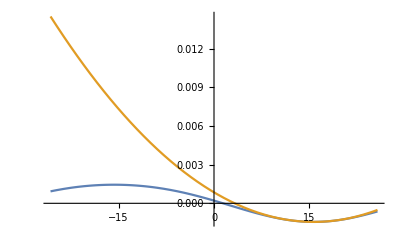

```mathematica
Negative beta potential stuff;
ClearAll["Global`*"]
ζ = 2; κ = .1; A = 1;
V[ξ_]:= 1/(24 ζ)κ^2 A^2(Cos[κ ξ])^2-κ^2 A/(2 Sqrt[6 ζ])Sin[κ ξ]
Vapprox[ξ_]:= (κ^4(A^2+A Sqrt[6 ζ])/(24 ζ))(ξ-π/(2κ))^2-A κ^2/(2 Sqrt[6 ζ])
Plot[{Re[V[x]],Re[Vapprox[x]]},{x,-Pi/(2 κ)-10,Pi/(2 κ)+10}]
```

```mathematica
Positive beta potential stuff;
ClearAll["Global`*"]
ζ = 2; κ = 1; A = 1;
V[ξ_]:= -1/(24 ζ)κ^2 A^2(Cos[κ ξ])^2-I κ^2 A/(2 Sqrt[6 ζ])Sin[κ ξ]
Vapprox[ξ_]:= (κ^4 A^2/(24 ζ))(ξ-I 6 Sqrt[ζ]/(κ A Sqrt[6]))^2-A^2 κ^2/(24 ζ)+κ^2/4
Plot[{Im[V[x]],Im[Vapprox[x]]},{x,-Pi/κ,Pi/κ}]
```

```mathematica
Interacting Two-Soliton movie;
```

```mathematica
ClearAll["Global`*"]
wow = Table[Rasterize[Plot[{8 Sech[2(x-16t)+.54930614]^2+2 Sech[(x-4t)-.54930614]^2,12(3+4Cosh[2x-8t]+Cosh[4x-64t])/(3 Cosh[x-28t]+Cosh[3x-36t])^2,0},{x,-19,19},PlotRange-> {-.3,10},Axes->False, PlotStyle->{ Blue,Orange,Black},PlotLegends->Placed[LineLegend[{"Independent","Interacting"},LegendMarkerSize->{{10,10}},LabelStyle->{FontSize->6},LegendLayout->{"Column",2}],{Right,Top}]],ImageResolution->400],{t,-1,1 ,.01}];
Export["Two Solitons.avi",wow ,FrameRate-> 60]
```

Two Solitons.avi

```mathematica
SystemOpen["Two Solitons.avi"]
Positive Beta PT symmetric Potential Stuff
```

```mathematica
ClearAll["Global`*"]
ClearAll["Global`*"]
V =(A^2 κ^4 (A^2 Cos[κ ξ]^4+24 ζ Sin[κ ξ]^2))/(576 ζ^2);
dV = -(A^2 κ^5 (A^2-24 ζ+A^2 Cos[2 κ ξ]) Sin[2 κ ξ])/(576 ζ^2);
d2V = -(A^2 κ^6 ((A^2-24 ζ) Cos[2 κ ξ]+A^2 Cos[4 κ ξ]))/(288 ζ^2);
```

```mathematica
FullSimplify[Solve[dV==0,ξ],{ζ>0,κ>0}]
```

```mathematica
{{ξ->ConditionalExpression[(π C[1])/κ,C[1]∈Integers]},{ξ->ConditionalExpression[(π+2 π C[1])/(2 κ),C[1]∈Integers]},{ξ->ConditionalExpression[(ArcTan[-1+(24 ζ)/A^2,-(4 √3 √((A^2-12 ζ) ζ))/A^2]+2 π C[1])/(2 κ),C[1]∈Integers]},{ξ->ConditionalExpression[(ArcTan[-1+(24 ζ)/A^2,(4 √3 √((A^2-12 ζ) ζ))/A^2]+2 π C[1])/(2 κ),C[1]∈Integers]}}
```

```mathematica
FullSimplify[1/(2 κ)ArcCos[24 ζ/A^2-1],ζ>0]
```

ArcCos[-1+(24 ζ)/A^2]/(2 κ)

# mKdV Lax Pairs and corresponding Dirac equation

```mathematica
ClearAll["Global`*"]
W = -1;
Lt = -I/Sqrt[W 6 ζ]({{0, D[u[x,t],t]}, {D[u[x,t],t], 0}})#&;
L1 = ({{ⅈ, 0}, {0, -ⅈ}})D[#,x]-I/Sqrt[W 6 ζ]({{0, u[x,t]}, {u[x,t], 0}})#&;
A1= -4ζ({{1, 0}, {0, 1}})D[#,{x,3}]-W({{u[x,t]^2, -D[u[x,t],x]Sqrt[6W ζ]}, {D[u[x,t],x]Sqrt[6W ζ], u[x,t]^2}}) D[#,x]-W/2({{2 u[x,t]D[u[x,t],x], -Sqrt[6W ζ] D[u[x,t],{x,2}]}, {Sqrt[6W ζ] D[u[x,t],{x,2}], 2 u[x,t]D[u[x,t],x]}})# &;
Ltf =  Lt[f[x]];
Lf = L1[f[x]];
Lf3 = D[Lf,{x,3}];
Lf1 = D[Lf,x];
Af = A1[f[x]];
Af1 = D[A1[f[x]],x];
MatrixForm[FullSimplify[Ltf + ({{ⅈ, 0}, {0, -ⅈ}}).Af1-I/Sqrt[6W ζ]({{0, u[x,t]}, {u[x,t], 0}}).Af-(-4ζ({{1, 0}, {0, 1}}).Lf3-W({{u[x,t]^2, -D[u[x,t],x]Sqrt[6ζ W]}, {D[u[x,t],x]Sqrt[6ζ W], u[x,t]^2}}) .Lf1-W/2({{2 u[x,t]D[u[x,t],x], -Sqrt[6ζ W] D[u[x,t],{x,2}]}, {Sqrt[6ζ W] D[u[x,t],{x,2}], 2 u[x,t]D[u[x,t],x]}}).Lf)],{ζ>0,ζ∈ Reals}]
```

(0 | -(ⅈ f[x] (u^(0,1)[x,t]-u[x,t]^2 u^(1,0)[x,t]+ζ u^(3,0)[x,t]))/(√6 √-ζ)
-(ⅈ f[x] (u^(0,1)[x,t]-u[x,t]^2 u^(1,0)[x,t]+ζ u^(3,0)[x,t]))/(√6 √-ζ) | 0)

# Dirac to Schrodinger equation transformation;

```mathematica
ClearAll["Global`*"]
w = -1; (*Sign of beta*)
Φ = 1/(Sqrt[6 ζ ] Sqrt[w])ϕ;
 dΦ =1/(Sqrt[6 ζ ] Sqrt[w])dϕ;
du1 = 1/I(I Φ u2+ Sqrt[e] u1);
du2 = -1/I(I Φ u1+  Sqrt[e] u2);
ddu1 =  1/I(I dΦ u2+I Φ du2+ Sqrt[e] du1);
ddu2 =  -1/I(I dΦ u1+I Φ  du1+ Sqrt[e] du2);
U1 = u1 + I u2;
U2 = u1 - I u2;
ddU1 = ddu1 + I ddu2;
ddU2 = ddu1 - I ddu2;
test1 = -ddU1+(-Φ^2-ⅈ dΦ)U1
test2 = -ddU2+ (-Φ^2+ⅈ dΦ)U2
FullSimplify[test1]
FullSimplify[test2]
```

(dϕ u1)/(√6 √ζ)+ⅈ √e (√e u2+(u1 ϕ)/(√6 √ζ))-(ⅈ ϕ (√e u1+(u2 ϕ)/(√6 √ζ)))/(√6 √ζ)+(u1+ⅈ u2) (-dϕ/(√6 √ζ)+ϕ^2/(6 ζ))+ⅈ ((dϕ u2)/(√6 √ζ)+(ⅈ ϕ (√e u2+(u1 ϕ)/(√6 √ζ)))/(√6 √ζ)-ⅈ √e (√e u1+(u2 ϕ)/(√6 √ζ)))

-(dϕ u1)/(√6 √ζ)-ⅈ √e (√e u2+(u1 ϕ)/(√6 √ζ))+(ⅈ ϕ (√e u1+(u2 ϕ)/(√6 √ζ)))/(√6 √ζ)+(u1-ⅈ u2) (dϕ/(√6 √ζ)+ϕ^2/(6 ζ))+ⅈ ((dϕ u2)/(√6 √ζ)+(ⅈ ϕ (√e u2+(u1 ϕ)/(√6 √ζ)))/(√6 √ζ)-ⅈ √e (√e u1+(u2 ϕ)/(√6 √ζ)))

e (u1+ⅈ u2)

e (u1-ⅈ u2)

# Solitary Wave Solutions of MkDv

```mathematica
u1 =  Sqrt[3 v]Tanh[Sqrt[v/(2ζ)](x+v t)+B];
u2 = Sqrt[6 v]Sech[Sqrt[v/ζ](x-v t)+B];
ClearAll["Global`*"]
b = -1;
(*u =((3 √2(a^2-v))/(a √2+ √(3v-a^2) Cosh[√(( a^2-v)/ζ) (t v+ x)])-a);*)
u = ( a+(3Sqrt[2](a^2-v))/(-a Sqrt[2] +   - Sqrt[3 v- a^2]Cosh[Sqrt[b(v-a^2)]/Sqrt[ζ](x-v b t)]));
(*u3 =Sqrt[v](1 - (12ζ)/(3ζ+2 v(x-v t)^2));*)
f = u;
FullSimplify[D[f,t] +b f^2 D[f,x]+ ζ D[f,{x,3}]]
```

0

# Recurrence time algebra;

```mathematica
w = 1; (*Sign of beta*)

A =(√(((-1+√(1+6 S w y^2)) Csc[(π y)/2]^2)/(w β)))/(√3); (*y is equal to 1/(N+1)*)
ζ = 1/(36 β);
L = a/y;
κ = π/L;
(*dv = 4 A κ^2 Sqrt[ζ/6];*)
dv = 4 Sqrt[A^2+A Sqrt[6ζ]] κ^2 Sqrt[ζ/6];
τ = L/dv;
t = (2 y^3)/(3 β a^3)τ;
FullSimplify[Series[t,{y,0,1}],S>0]
```

3/(π √(√(3/2) π √S+6 S))+O[y]^2

```mathematica
ϕ = -Sqrt[3 v]Tanh[Sqrt[v/(2 ζ)]ξ];
FullSimplify[1/(6 ζ)ϕ^2-1/Sqrt[6 ζ] D[ϕ,ξ],{v>0,ζ>0}]
```

v/(2 ζ)

```mathematica
3/(2 36)
```

1/24

```mathematica
ClearAll["Global`*"]
u =√6 √mod √ζ c[1] JacobiSN[phase+x c[1]+t ζ c[1]^3+mod t ζ c[1]^3,mod];
FullSimplify[D[u,t]-u^2 D[u,x]+D[u,{x,3}]]
```

√6 √mod (-1+ζ) √ζ c[1]^4 JacobiCN[phase+x c[1]+(1+mod) t ζ c[1]^3,mod] JacobiDN[phase+x c[1]+(1+mod) t ζ c[1]^3,mod] (-5+mod+6 JacobiDN[phase+x c[1]+(1+mod) t ζ c[1]^3,mod]^2)

## Bright Soliton

```mathematica
ClearAll["Global`*"]
b = Sqrt[6 a^2-v]/(2 a);
FullSimplify[-a(1-(2 b^2)/(1+Sqrt[1-b^2]Cosh[2 a b(x+v t)])),{a>0,v>0}]
```

```mathematica
FullSimplify[(-a Sqrt[6]+(Sqrt[6](6 a^2-v))/(2 a+ √(v-2  a^2) Cosh[√((6  a^2-v)/ζ) (t v+ x)]))]
```

√6 (-a+(6 a^2-v)/(2 a+√(-2 a^2+v) Cosh[(t v+x) √((6 a^2-v)/ζ)]))

```mathematica
Sqrt[3/2] 1/6
```

1/(2 √6)

```mathematica
A = 2/Pi Sqrt[S/B];
FullSimplify[Sqrt[6]/(Pi^2 Sqrt[B A^2+A Sqrt[B/6]]),{B>0,S>0}]
```

3/(π √(√(3/2) π √S+6 S))

## Blow Up

```mathematica
Clear[m1,m2,n,A]
pos = (-A +√(4-3 A^2 ))/2;
neg = (-A -√(4-3 A^2 ))/2;
Simplify[m1  A+m2 pos+(n+1-m1-m2)neg]
FullSimplify[Solve[m1  pos+m2 neg+(n+1-m1-m2)A==0,A]]
```

1/2 (A (-1+3 m1-n)+√(4-3 A^2) (-1+m1+2 m2-n))

{{A→(-m1+m2)/(√(3 m1^2+3 m2^2+3 m1 (-1+m2-n)-3 m2 (1+n)+(1+n)^2))},{A→(m1-m2)/(√(3 m1^2+3 m2^2+3 m1 (-1+m2-n)-3 m2 (1+n)+(1+n)^2))}}

```mathematica
m2=0;
m1 = 1;

A=(m1-m2)/(√(3 m1^2+3 m2^2+3 m1 (-1+m2-n)-3 m2 (1+n)+(1+n)^2));
pos = (-A+√(4-3 A^2))/2;
neg = (-A-√(4-3 A^2))/2;

V[x_] :=x^2/2-x^4/4;
En =  Simplify[m1*V[pos]+m2*V[neg]+(n+1-m1-m2)*V[A]]
```

(1+2 n^4-√((-1+2 n)^2/(1-n+n^2)) √(1-n+n^2))/(8 (1-n+n^2)^2)

```mathematica
NMinimize[{(m1 (-1001+m1+2 m2)^2 (1002001+5 m1^2+2 m1 (-2002+m2)-2002 m2+2 m2^2))/(4 (1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2)^2)+1/64 (1001-m1-m2) (√((1001-3 m1)^2/(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2))-(-1001+m1+2 m2)/(√(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2)))^2 (8-(√((1001-3 m1)^2/(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2))-(-1001+m1+2 m2)/(√(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2)))^2)+1/64 m2 (√((1001-3 m1)^2/(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2))+(-1001+m1+2 m2)/(√(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2)))^2 (8-(√((1001-3 m1)^2/(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2))+(-1001+m1+2 m2)/(√(1002001+3 m1^2+3 m1 (-1001+m2)-3003 m2+3 m2^2)))^2),0<m1+m2<1001&& m1>0 && m2>0,m1∈ Integers,m2∈ Integers},{m1,m2},MaxIterations->10000]
```

NMinimize::ivar: 1 is not a valid variable.

NMinimize[{249750000000250/998002998001,False,True,True},{1,0},MaxIterations→10000]

```mathematica
DensityPlot[((1-m1-2 m2+n)^2 (5 m1^2+2 m2^2-2 m2 (1+n)+(1+n)^2+2 m1 (m2-2 (1+n))))/(4 (3 m1^2+3 m2^2+3 m1 (-1+m2-n)-3 m2 (1+n)+(1+n)^2)^2),{m1,0,100/2},{m2,0,100/2},PlotLegends-> Automatic]
```

-Graphics-